# Notebook for : Exact Spacetimes in Einstein’s General Relativity by Griffiths and Podolsky Chapter 4: De Sitter

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
March 27, 2022

```mathematica
(* Problem with the symbolize - need it for dtReplace to work... *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book and Related

```mathematica
Hyperlink["Exact Space-Times in Einstein's General Relativity",
"https://www.cambridge.org/core/books/exact-spacetimes-in-einsteins-general-relativity/48896A8900897F53BDAA917456E884D6"]
```

[Exact Space-Times in Einstein's General Relativity](https://www.cambridge.org/core/books/exact-spacetimes-in-einsteins-general-relativity/48896A8900897F53BDAA917456E884D6)

```mathematica
Hyperlink["Exact Space-Times in Einstein's General Relativity Front Matter",
"https://assets.cambridge.org/97805218/89278/frontmatter/9780521889278_frontmatter.pdf"]
```

[Exact Space-Times in Einstein's General Relativity Front Matter](https://assets.cambridge.org/97805218/89278/frontmatter/9780521889278_frontmatter.pdf)

```mathematica
(*  Equation 4.17 in book corresponds to equation 2 in paper *) 

Hyperlink["Nonexpanding Impulsive Gravitational Waves With An Arbitrary Cosmological Constant by Podolsky and Griffiths","https://arxiv.org/abs/gr-qc/9908008"]
```

[Nonexpanding Impulsive Gravitational Waves With An Arbitrary Cosmological Constant by Podolsky and Griffiths](https://arxiv.org/abs/gr-qc/9908008)

```mathematica
Hyperlink["Understanding Exact Spacetimes CQG plus",
"https://cqgplus.com/2018/08/20/understanding-exact-space-times/"]
```

[Understanding Exact Spacetimes CQG plus](https://cqgplus.com/2018/08/20/understanding-exact-space-times/)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[Subscript[Z, 0]],
 PasteButton[Subscript[Z, 1]] , 
PasteButton[Subscript[Z, 2]] ,
PasteButton[Subscript[Z, 3]] ,
PasteButton[Subscript[Z, 4]] ,
PasteButton[Subscript[R, 0]] , 
PasteButton[Subscript[t,-1]]
}]
```

rzudu_shm39FrontEndObject[LinkObject["rzudu_shm", 3, 1]]39Untitled-3

```mathematica
Symbolize[Subscript[Z, 0]]
Symbolize[Subscript[Z, 1]]
Symbolize[Subscript[Z, 2]]
Symbolize[Subscript[Z, 3]]
Symbolize[Subscript[Z, 4]]
Symbolize[Subscript[η, 0]]
Symbolize[Subscript[R, 0]]
Symbolize[Subscript[t, -1]]
Symbolize[Subscript[t, b]]
Symbolize[Subscript[z, b]]
Symbolize[Subscript[t, k]]
Symbolize[Subscript[z, k]]
```

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[Subscript[Z, 0]] -> Subscript[dZ, 0] ,
Dt[Subscript[Z, 1]] -> Subscript[dZ, 1] ,
Dt[Subscript[Z, 2]]-> Subscript[dZ, 2] ,
Dt[Subscript[Z, 3]]-> Subscript[dZ, 3] ,
Dt[Subscript[Z, 4]] -> Subscript[dZ, 4] ,
Dt[Subscript[η, 0]]-> Subscript[dη, 0] , 
Dt[Subscript[t, -1]]-> Subscript[dt, -1] , 
Dt[Subscript[t, b]]-> Subscript[dt, b] , 
Dt[Subscript[z, b]]-> Subscript[dz, b] , 
Dt[Subscript[t, k]]-> Subscript[dt, k] , 
Dt[Subscript[z, k]]-> Subscript[dz, k] , 
Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z] -> dz , 
Dt[r]-> dr , 
Dt[s]-> ds , 
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv , 
 Dt[z]-> dz , 
Dt[τ]-> dτ , 
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[R]-> dR, 
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[X]-> dX , 
Dt[Y]-> dY , 
Dt[Z]-> dZ , 
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ , 
Dt[ζ]-> dζ , 
Dt[ζbar]-> dζbar ,
Dt[𝒰]-> d𝒰 , 
Dt[𝒱]-> d𝒱 ,  
Dt[ξ]-> dξ , 
Dt[ξbar]-> dξbar 
};
dtReplace // TableForm
```

Dt[Z] Subscript^(1,0)[Z,0]→dZ_0
Dt[Z] Subscript^(1,0)[Z,1]→dZ_1
Dt[Z] Subscript^(1,0)[Z,2]→dZ_2
Dt[Z] Subscript^(1,0)[Z,3]→dZ_3
Dt[Z] Subscript^(1,0)[Z,4]→dZ_4
Dt[η] Subscript^(1,0)[η,0]→dη_0
Dt[t] Subscript^(1,0)[t,-1]→dt_-1
Dt[b] Subscript^(0,1)[t,b]+Dt[t] Subscript^(1,0)[t,b]→dt_b
Dt[b] Subscript^(0,1)[z,b]+Dt[z] Subscript^(1,0)[z,b]→dz_b
Dt[k] Subscript^(0,1)[t,k]+Dt[t] Subscript^(1,0)[t,k]→dt_k
Dt[k] Subscript^(0,1)[z,k]+Dt[z] Subscript^(1,0)[z,k]→dz_k
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[r]→dr
Dt[s]→ds
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[z]→dz
Dt[τ]→dτ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[R]→dR
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ
Dt[ζ]→dζ
Dt[ζbar]→dζbar
Dt[𝒰]→d𝒰
Dt[𝒱]→d𝒱
Dt[ξ]→dξ
Dt[ξbar]→dξbar

```mathematica
Subscript[R, 0]/:Dt[Subscript[R, 0]]=0  ; (* Subscript[R, 0] is a constant, it's differential is zero *) 
M/:Dt[M]=0  ;   (*  we use M for mass and reserve m for a null vector *)
𝒞 /:Dt[𝒞]= 0 ; (* Regular C is protected use [esc]scC[esc].  See 3.12 *)
a /:Dt[a]= 0 ;   
Λ/:Dt[Λ]= 0 ;   (* 3.13 *)
```

TagSet::sym: Argument R_0 at position 1 is expected to be a symbol.

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 4.1: de Sitter Manifold as Hyperboloid Embedded in 5D Minkowski

```mathematica
Clear[eq4pt1]
eq4pt1 = {
- Subscript[Z, 0]^2+ Subscript[Z, 1]^2+Subscript[Z, 2]^2+Subscript[Z, 3]^2+Subscript[Z, 4]^2== a^2 ,
 a== √(3/Λ)
} ;
eq4pt1  // TableForm
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2
a==√3 √(1/Λ)

```mathematica
Clear[eq4pt2]
eq4pt2 = 
 - Subscript[dZ, 0]^2 + Subscript[dZ, 1]^2+ Subscript[dZ, 2]^2+Subscript[dZ, 3]^2+Subscript[dZ, 4]^2
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

```mathematica
Clear[metric4pt2]
metric4pt2 = 
lineToMetric[eq4pt2,{Subscript[dZ, 0],Subscript[dZ, 1],Subscript[dZ, 2],Subscript[dZ, 3],Subscript[dZ, 4]} ]  ;
metric4pt2 // MatrixForm
```

(-1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

## Line Element and Metric 4.4: de Sitter in FRLW Form

```mathematica
Clear[eq4pt3]
eq4pt3 = { 
Subscript[Z, 0]==  a Sinh[t/a] ,
Subscript[Z, 1]==  a Cosh[t/a] Cos[χ] ,
Subscript[Z, 2]==  a Cosh[t/a] Sin[χ] Cos[θ] ,
Subscript[Z, 3]==  a Cosh[t/a] Sin[χ] Sin[θ] Cos[ϕ] ,
Subscript[Z, 4]== a Cosh[t/a] Sin[χ] Sin[θ] Sin[ϕ]
} ;
eq4pt3  /. Equal-> Rule // TableForm
```

Z_0→a Sinh[t/a]
Z_1→a Cos[χ] Cosh[t/a]
Z_2→a Cos[θ] Cosh[t/a] Sin[χ]
Z_3→a Cos[ϕ] Cosh[t/a] Sin[θ] Sin[χ]
Z_4→a Cosh[t/a] Sin[θ] Sin[ϕ] Sin[χ]

```mathematica
( Dt[eq4pt3] /. dtReplace /. Equal-> Rule )  // TableForm
```

dZ_0→dt Cosh[t/a]
dZ_1→-a dχ Cosh[t/a] Sin[χ]+dt Cos[χ] Sinh[t/a]
dZ_2→a dχ Cos[θ] Cos[χ] Cosh[t/a]-a dθ Cosh[t/a] Sin[θ] Sin[χ]+dt Cos[θ] Sin[χ] Sinh[t/a]
dZ_3→a dχ Cos[ϕ] Cos[χ] Cosh[t/a] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Cosh[t/a] Sin[χ]-a dϕ Cosh[t/a] Sin[θ] Sin[ϕ] Sin[χ]+dt Cos[ϕ] Sin[θ] Sin[χ] Sinh[t/a]
dZ_4→a dχ Cos[χ] Cosh[t/a] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Cosh[t/a] Sin[θ] Sin[χ]+a dθ Cos[θ] Cosh[t/a] Sin[ϕ] Sin[χ]+dt Sin[θ] Sin[ϕ] Sin[χ] Sinh[t/a]

```mathematica
(* Just a quick check to make sure we've done the transformation correctly *) 

eq4pt1[[1]]
eq4pt1[[1]] /. (eq4pt3  /. Equal-> Rule)
eq4pt1[[1]] /. (eq4pt3  /. Equal-> Rule) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

a^2 Cos[χ]^2 Cosh[t/a]^2+a^2 Cos[θ]^2 Cosh[t/a]^2 Sin[χ]^2+a^2 Cos[ϕ]^2 Cosh[t/a]^2 Sin[θ]^2 Sin[χ]^2+a^2 Cosh[t/a]^2 Sin[θ]^2 Sin[ϕ]^2 Sin[χ]^2-a^2 Sinh[t/a]^2==a^2

True

```mathematica
eq4pt2
eq4pt2 /. ( Dt[eq4pt3] /. dtReplace /. Equal-> Rule )
eq4pt2 /. ( Dt[eq4pt3] /. dtReplace /. Equal-> Rule ) // Expand // Simplify
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

-dt^2 Cosh[t/a]^2+(-a dχ Cosh[t/a] Sin[χ]+dt Cos[χ] Sinh[t/a])^2+(a dχ Cos[θ] Cos[χ] Cosh[t/a]-a dθ Cosh[t/a] Sin[θ] Sin[χ]+dt Cos[θ] Sin[χ] Sinh[t/a])^2+(a dχ Cos[ϕ] Cos[χ] Cosh[t/a] Sin[θ]+a dθ Cos[θ] Cos[ϕ] Cosh[t/a] Sin[χ]-a dϕ Cosh[t/a] Sin[θ] Sin[ϕ] Sin[χ]+dt Cos[ϕ] Sin[θ] Sin[χ] Sinh[t/a])^2+(a dχ Cos[χ] Cosh[t/a] Sin[θ] Sin[ϕ]+a dϕ Cos[ϕ] Cosh[t/a] Sin[θ] Sin[χ]+a dθ Cos[θ] Cosh[t/a] Sin[ϕ] Sin[χ]+dt Sin[θ] Sin[ϕ] Sin[χ] Sinh[t/a])^2

1/32 (-32 dt^2+8 a^2 dθ^2+4 a^2 dϕ^2+16 a^2 dχ^2-4 a^2 dϕ^2 Cos[2 θ]+2 a^2 dϕ^2 Cos[2 (θ-χ)]-8 a^2 dθ^2 Cos[2 χ]-4 a^2 dϕ^2 Cos[2 χ]+2 a^2 dϕ^2 Cos[2 (θ+χ)]+4 a^2 (2 dθ^2+dϕ^2+4 dχ^2) Cosh[(2 t)/a]-2 a^2 dϕ^2 Cosh[(2 t)/a-2 ⅈ θ]-2 a^2 dϕ^2 Cosh[(2 t)/a+2 ⅈ θ]+a^2 dϕ^2 Cosh[(2 t)/a+2 ⅈ (θ-χ)]-4 a^2 dθ^2 Cosh[(2 t)/a-2 ⅈ χ]-2 a^2 dϕ^2 Cosh[(2 t)/a-2 ⅈ χ]-4 a^2 dθ^2 Cosh[(2 t)/a+2 ⅈ χ]-2 a^2 dϕ^2 Cosh[(2 t)/a+2 ⅈ χ]+a^2 dϕ^2 Cosh[(2 t)/a-2 ⅈ θ+2 ⅈ χ]+a^2 dϕ^2 Cosh[(2 t)/a-2 ⅈ (θ+χ)]+a^2 dϕ^2 Cosh[(2 t)/a+2 ⅈ (θ+χ)])

```mathematica
Clear[metric4pt4]
metric4pt4 = 
lineToMetric[ (eq4pt2 /. ( Dt[eq4pt3] /. dtReplace /. Equal-> Rule ) ) , {dt,dχ,dθ,dϕ}] // Expand // FullSimplify  ;
metric4pt4 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Cosh[t/a]^2 | 0 | 0
0 | 0 | a^2 Cosh[t/a]^2 Sin[χ]^2 | 0
0 | 0 | 0 | a^2 Cosh[t/a]^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
Clear[eq4pt4]
eq4pt4 = 
Collect[ metricToLine[metric4pt4, {dt,dχ,dθ,dϕ}],a^2 Cosh[t/a]^2]
```

-dt^2+a^2 Cosh[t/a]^2 (dχ^2+dθ^2 Sin[χ]^2+dϕ^2 Sin[θ]^2 Sin[χ]^2)

## Line Element and Metric 4.6: de Sitter Conformal to Einstein Static

```mathematica
Clear[eq4pt5]
eq4pt5 = 
Sin[η]== Sech[t/a]
```

Sin[η]==Sech[t/a]

```mathematica
Flatten[Solve[ eq4pt5,t]][[2]] /. C[1]-> 0
```

t→a ArcCosh[Csc[η]]

```mathematica
Dt[( Flatten[Solve[ eq4pt5,t]][[2]] /. C[1]-> 0 )] /. dtReplace
```

dt→-(a dη Cot[η] Csc[η])/(√(-1+Csc[η]) √(1+Csc[η]))

```mathematica
eq4pt4
eq4pt4 /. ( Flatten[Solve[ eq4pt5,t]][[2]] /. C[1]-> 0 )
eq4pt4 /. ( Flatten[Solve[ eq4pt5,t]][[2]] /. C[1]-> 0 ) /. ( Dt[( Flatten[Solve[ eq4pt5,t]][[2]] /. C[1]-> 0 )] /. dtReplace )
```

-dt^2+a^2 Cosh[t/a]^2 (dχ^2+dθ^2 Sin[χ]^2+dϕ^2 Sin[θ]^2 Sin[χ]^2)

-dt^2+a^2 Csc[η]^2 (dχ^2+dθ^2 Sin[χ]^2+dϕ^2 Sin[θ]^2 Sin[χ]^2)

-(a^2 dη^2 Cot[η]^2 Csc[η]^2)/((-1+Csc[η]) (1+Csc[η]))+a^2 Csc[η]^2 (dχ^2+dθ^2 Sin[χ]^2+dϕ^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
Clear[metric4pt6]
metric4pt6 = 
lineToMetric[eq4pt4 /. ( Flatten[Solve[ eq4pt5,t]][[2]] /. C[1]-> 0 ) /. ( Dt[( Flatten[Solve[ eq4pt5,t]][[2]] /. C[1]-> 0 )] /. dtReplace ),{ dη, dχ, dθ, dϕ } ] // Expand // Simplify  ;
metric4pt6 // MatrixForm
```

(-a^2 Csc[η]^2 | 0 | 0 | 0
0 | a^2 Csc[η]^2 | 0 | 0
0 | 0 | a^2 Csc[η]^2 Sin[χ]^2 | 0
0 | 0 | 0 | a^2 Csc[η]^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
Clear[eq4pt6]
eq4pt6 = 
Collect[ metricToLine[metric4pt6,{ dη, dχ, dθ, dϕ } ],{ a^2 Csc[η]^2 ,Sin[χ]^2}]
```

a^2 Csc[η]^2 (-dη^2+dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

## Line Element and Metric 4.9: de Sitter Spherical Coordinates

```mathematica
Clear[eq4pt8]
eq4pt8 = { 
Subscript[Z, 0] ==   √(a^2-R^2)Sinh[T/a],
Subscript[Z, 1] ==  √(a^2-R^2)Cosh[T/a] , 
Subscript[Z, 2] ==  R Cos[θ] ,
Subscript[Z, 3] ==   R Sin[θ] Cos[ϕ] ,
Subscript[Z, 4] ==   R Sin[θ] Sin[ϕ]
} ;
( eq4pt8 /. Equal-> Rule )  // TableForm
```

Z_0→√(a^2-R^2) Sinh[T/a]
Z_1→√(a^2-R^2) Cosh[T/a]
Z_2→R Cos[θ]
Z_3→R Cos[ϕ] Sin[θ]
Z_4→R Sin[θ] Sin[ϕ]

```mathematica
(* Just a quick check to make sure we've done the transformation correctly *) 

eq4pt1[[1]] 
eq4pt1[[1]] /. ( eq4pt8 /. Equal-> Rule )
eq4pt1[[1]] /. ( eq4pt8 /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

R^2 Cos[θ]^2+(a^2-R^2) Cosh[T/a]^2+R^2 Cos[ϕ]^2 Sin[θ]^2+R^2 Sin[θ]^2 Sin[ϕ]^2-(a^2-R^2) Sinh[T/a]^2==a^2

True

```mathematica
( Dt[eq4pt8 ] /. dtReplace /. Equal-> Rule  // Expand // Simplify )  // TableForm
```

dZ_0→(dT (a^2-R^2) Cosh[T/a]-a dR R Sinh[T/a])/(a √(a^2-R^2))
dZ_1→(-a dR R Cosh[T/a]+dT (a^2-R^2) Sinh[T/a])/(a √(a^2-R^2))
dZ_2→dR Cos[θ]-dθ R Sin[θ]
dZ_3→dθ R Cos[θ] Cos[ϕ]+Sin[θ] (dR Cos[ϕ]-dϕ R Sin[ϕ])
dZ_4→dϕ R Cos[ϕ] Sin[θ]+(dθ R Cos[θ]+dR Sin[θ]) Sin[ϕ]

```mathematica
eq4pt1[[2]] /. Equal-> Rule
```

a→√3 √(1/Λ)

```mathematica
eq4pt2
eq4pt2 /. ( Dt[eq4pt8 ] /. dtReplace /. Equal-> Rule  // Expand // Simplify )
eq4pt2 /. ( Dt[eq4pt8 ] /. dtReplace /. Equal-> Rule  // Expand // Simplify ) /. ( eq4pt1[[2]] /. Equal-> Rule )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

(dR Cos[θ]-dθ R Sin[θ])^2+(dϕ R Cos[ϕ] Sin[θ]+(dθ R Cos[θ]+dR Sin[θ]) Sin[ϕ])^2+(dθ R Cos[θ] Cos[ϕ]+Sin[θ] (dR Cos[ϕ]-dϕ R Sin[ϕ]))^2-((dT (a^2-R^2) Cosh[T/a]-a dR R Sinh[T/a])^2)/(a^2 (a^2-R^2))+((-a dR R Cosh[T/a]+dT (a^2-R^2) Sinh[T/a])^2)/(a^2 (a^2-R^2))

(dR Cos[θ]-dθ R Sin[θ])^2+(dϕ R Cos[ϕ] Sin[θ]+(dθ R Cos[θ]+dR Sin[θ]) Sin[ϕ])^2+(dθ R Cos[θ] Cos[ϕ]+Sin[θ] (dR Cos[ϕ]-dϕ R Sin[ϕ]))^2+(Λ (-√3 dR R √(1/Λ) Cosh[T/(√3 √(1/Λ))]+dT (-R^2+3/Λ) Sinh[T/(√3 √(1/Λ))])^2)/(3 (-R^2+3/Λ))-(Λ (dT (-R^2+3/Λ) Cosh[T/(√3 √(1/Λ))]-√3 dR R √(1/Λ) Sinh[T/(√3 √(1/Λ))])^2)/(3 (-R^2+3/Λ))

```mathematica
(* Reduce second component by hand... *) 

Clear[metric4pt9]
metric4pt9 = 
lineToMetric[ ( eq4pt2 /. ( Dt[eq4pt8 ] /. dtReplace /. Equal-> Rule  // Expand // Simplify ) /. ( eq4pt1[[2]] /. Equal-> Rule ) ) , {dT,dR,dθ,dϕ}] // Expand // Simplify  ;
metric4pt9 // MatrixForm
```

(-1+(R^2 Λ)/3 | 0 | 0 | 0
0 | 3/(3-R^2 Λ) | 0 | 0
0 | 0 | R^2 | 0
0 | 0 | 0 | R^2 Sin[θ]^2)

```mathematica
Clear[eq4pt9]
eq4pt9 = 
metricToLine[metric4pt9,   {dT,dR,dθ,dϕ}]
```

dθ^2 R^2+(3 dR^2)/(3-R^2 Λ)+dT^2 (-1+(R^2 Λ)/3)+dϕ^2 R^2 Sin[θ]^2

## Line Element and Metric 4.10: de Sitter Spherical Coordinates

```mathematica
Clear[eq4pt9a] (* Equation not numbered in text *) 
eq4pt9a = 
R ==  a Sin[χ]
```

R==a Sin[χ]

```mathematica
eq4pt9a /. Equal-> Rule
```

R→a Sin[χ]

```mathematica
Dt[eq4pt9a/. Equal-> Rule ] /. dtReplace
```

dR→a dχ Cos[χ]

```mathematica
eq4pt9
eq4pt9 /. (eq4pt9a /. Equal-> Rule  )
eq4pt9 /. (eq4pt9a /. Equal-> Rule  ) /. ( Dt[eq4pt9a/. Equal-> Rule ] /. dtReplace ) /. Flatten[Solve[ eq4pt1[[2]], Λ]][[1]] 
eq4pt9 /. (eq4pt9a /. Equal-> Rule  ) /. ( Dt[eq4pt9a/. Equal-> Rule ] /. dtReplace ) /. Flatten[Solve[ eq4pt1[[2]], Λ]][[1]]  // Simplify
```

dθ^2 R^2+(3 dR^2)/(3-R^2 Λ)+dT^2 (-1+(R^2 Λ)/3)+dϕ^2 R^2 Sin[θ]^2

a^2 dθ^2 Sin[χ]^2+a^2 dϕ^2 Sin[θ]^2 Sin[χ]^2+(3 dR^2)/(3-a^2 Λ Sin[χ]^2)+dT^2 (-1+1/3 a^2 Λ Sin[χ]^2)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

a^2 dθ^2 Sin[χ]^2+a^2 dϕ^2 Sin[θ]^2 Sin[χ]^2+(3 a^2 dχ^2 Cos[χ]^2)/(3-3 Sin[χ]^2)+dT^2 (-1+Sin[χ]^2)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

-dT^2+a^2 dχ^2+(dT^2+a^2 dθ^2+a^2 dϕ^2 Sin[θ]^2) Sin[χ]^2

```mathematica
Clear[metric4pt10]
metric4pt10 = 
lineToMetric[ (  eq4pt9 /. (eq4pt9a /. Equal-> Rule  ) /. ( Dt[eq4pt9a/. Equal-> Rule ] /. dtReplace ) /. Flatten[Solve[ eq4pt1[[2]], Λ]][[1]]  // Simplify)  , {dT,dχ,dθ,dϕ}]  // Simplify  ;
metric4pt10 // MatrixForm
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(-Cos[χ]^2 | 0 | 0 | 0
0 | a^2 | 0 | 0
0 | 0 | a^2 Sin[χ]^2 | 0
0 | 0 | 0 | a^2 Sin[θ]^2 Sin[χ]^2)

```mathematica
Clear[eq4pt10]
eq4pt10 = 
Collect[ metricToLine[metric4pt10, {dT,dχ,dθ,dϕ}] ,{a^2,Sin[χ]^2}]
```

-dT^2 Cos[χ]^2+a^2 (dχ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sin[χ]^2)

## Line Element and Metric 4.12: Conformally Flat Coordinates

```mathematica
Clear[eq4pt12]
eq4pt12 = { 
Subscript[Z, 0] ==  (a^2+s)/(2 Subscript[η, 0]) , 
Subscript[Z, 1] ==  (a^2-s)/(2 Subscript[η, 0])  ,
Subscript[Z, 2] ==  a (x/Subscript[η, 0]) ,
Subscript[Z, 3] ==  a (y/Subscript[η, 0]) ,
Subscript[Z, 4] ==  a (z/Subscript[η, 0])
} ;
( eq4pt12  /. Equal-> Rule )   // TableForm
```

Z_0→(a^2+s)/(2 η_0)
Z_1→(a^2-s)/(2 η_0)
Z_2→(a x)/η_0
Z_3→(a y)/η_0
Z_4→(a z)/η_0

```mathematica
Clear[eq4pt12a]
eq4pt12a =
 s ==  - Subscript[η, 0]^2+x^2+y^2+z^2
```

s==x^2+y^2+z^2-η_0^2

```mathematica
(* Just a quick check to make sure we've done the transformation correctly *) 

eq4pt1[[1]]
eq4pt1[[1]] /. ( eq4pt12  /. Equal-> Rule )
eq4pt1[[1]] /. ( eq4pt12  /. Equal-> Rule ) /. ( eq4pt12a  /. Equal-> Rule )
eq4pt1[[1]] /. ( eq4pt12  /. Equal-> Rule ) /. ( eq4pt12a  /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

((a^2-s)^2)/(4 η_0^2)-((a^2+s)^2)/(4 η_0^2)+(a^2 x^2)/η_0^2+(a^2 y^2)/η_0^2+(a^2 z^2)/η_0^2==a^2

(a^2 x^2)/η_0^2+(a^2 y^2)/η_0^2+(a^2 z^2)/η_0^2-((a^2+x^2+y^2+z^2-η_0^2)^2)/(4 η_0^2)+((a^2-x^2-y^2-z^2+η_0^2)^2)/(4 η_0^2)==a^2

True

```mathematica
Dt[( eq4pt12  /. Equal-> Rule )  ] /. dtReplace // TableForm
```

dZ_0→ds/(2 η_0)-((a^2+s) dη_0)/(2 η_0^2)
dZ_1→-ds/(2 η_0)-((a^2-s) dη_0)/(2 η_0^2)
dZ_2→(a dx)/η_0-(a x dη_0)/η_0^2
dZ_3→(a dy)/η_0-(a y dη_0)/η_0^2
dZ_4→(a dz)/η_0-(a z dη_0)/η_0^2

```mathematica
(eq4pt12a  /. Equal-> Rule )
```

s→x^2+y^2+z^2-η_0^2

```mathematica
( Dt[ (eq4pt12a  /. Equal-> Rule )] /. dtReplace )
```

ds→2 dx x+2 dy y+2 dz z-2 η_0 dη_0

```mathematica
( Dt[( eq4pt12  /. Equal-> Rule )  ] /. dtReplace ) /. (eq4pt12a  /. Equal-> Rule ) // TableForm
```

dZ_0→ds/(2 η_0)-((a^2+x^2+y^2+z^2-η_0^2) dη_0)/(2 η_0^2)
dZ_1→-ds/(2 η_0)-((a^2-x^2-y^2-z^2+η_0^2) dη_0)/(2 η_0^2)
dZ_2→(a dx)/η_0-(a x dη_0)/η_0^2
dZ_3→(a dy)/η_0-(a y dη_0)/η_0^2
dZ_4→(a dz)/η_0-(a z dη_0)/η_0^2

```mathematica
( Dt[( eq4pt12  /. Equal-> Rule )  ] /. dtReplace ) /. (eq4pt12a  /. Equal-> Rule )  /. ( Dt[ (eq4pt12a  /. Equal-> Rule )] /. dtReplace )  // TableForm
```

dZ_0→-((a^2+x^2+y^2+z^2-η_0^2) dη_0)/(2 η_0^2)+(2 dx x+2 dy y+2 dz z-2 η_0 dη_0)/(2 η_0)
dZ_1→-((a^2-x^2-y^2-z^2+η_0^2) dη_0)/(2 η_0^2)-(2 dx x+2 dy y+2 dz z-2 η_0 dη_0)/(2 η_0)
dZ_2→(a dx)/η_0-(a x dη_0)/η_0^2
dZ_3→(a dy)/η_0-(a y dη_0)/η_0^2
dZ_4→(a dz)/η_0-(a z dη_0)/η_0^2

```mathematica
eq4pt2
eq4pt2 /. ( Dt[( eq4pt12  /. Equal-> Rule )  ] /. dtReplace ) /. (eq4pt12a  /. Equal-> Rule )  /. ( Dt[ (eq4pt12a  /. Equal-> Rule )] /. dtReplace ) 
eq4pt2 /. ( Dt[( eq4pt12  /. Equal-> Rule )  ] /. dtReplace ) /. (eq4pt12a  /. Equal-> Rule )  /. ( Dt[ (eq4pt12a  /. Equal-> Rule )] /. dtReplace )  // Expand // Simplify
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

((a dx)/η_0-(a x dη_0)/η_0^2)^2+((a dy)/η_0-(a y dη_0)/η_0^2)^2+((a dz)/η_0-(a z dη_0)/η_0^2)^2+(-((a^2-x^2-y^2-z^2+η_0^2) dη_0)/(2 η_0^2)-(2 dx x+2 dy y+2 dz z-2 η_0 dη_0)/(2 η_0))^2-(-((a^2+x^2+y^2+z^2-η_0^2) dη_0)/(2 η_0^2)+(2 dx x+2 dy y+2 dz z-2 η_0 dη_0)/(2 η_0))^2

(a^2 (dx^2+dy^2+dz^2-dη_0^2))/η_0^2

```mathematica
Clear[metric4pt13]
metric4pt13  = 
lineToMetric[( eq4pt2 /. ( Dt[( eq4pt12  /. Equal-> Rule )  ] /. dtReplace ) /. (eq4pt12a  /. Equal-> Rule )  /. ( Dt[ (eq4pt12a  /. Equal-> Rule )] /. dtReplace )  // Expand // Simplify  ) , {Subscript[dη, 0] , dx,dy,dz} ]  ;
metric4pt13 // MatrixForm
```

(-a^2/η_0^2 | 0 | 0 | 0
0 | a^2/η_0^2 | 0 | 0
0 | 0 | a^2/η_0^2 | 0
0 | 0 | 0 | a^2/η_0^2)

```mathematica
Clear[eq4pt13]
eq4pt13 = 
Collect[ metricToLine[metric4pt13 , {Subscript[dη, 0] , dx,dy,dz} ] , a^2/Subscript[η, 0]^2]
```

(a^2 (dx^2+dy^2+dz^2-dη_0^2))/η_0^2

## Line Element and Metric 4.16: Negative Spatial Curvature

```mathematica
Clear[eq4pt15]
eq4pt15 = { 
Subscript[Z, 0] ==  a Sinh[Subscript[t, -1]/a] Cosh[ρ],
Subscript[Z, 1] ==  a Cosh[Subscript[t, -1]/a] ,
Subscript[Z, 2] ==   a Sinh[Subscript[t, -1]/a] Sinh[ρ] Cos[θ],
Subscript[Z, 3] ==  a Sinh[Subscript[t, -1]/a] Sinh[ρ] Sin[θ] Cos[ϕ],
Subscript[Z, 4] ==    a Sinh[Subscript[t, -1]/a] Sinh[ρ] Sin[θ] Sin[ϕ]
} ;
( eq4pt15 /. Equal-> Rule )  // TableForm
```

Z_0→a Cosh[ρ] Sinh[(t_-1)/a]
Z_1→a Cosh[(t_-1)/a]
Z_2→a Cos[θ] Sinh[ρ] Sinh[(t_-1)/a]
Z_3→a Cos[ϕ] Sin[θ] Sinh[ρ] Sinh[(t_-1)/a]
Z_4→a Sin[θ] Sin[ϕ] Sinh[ρ] Sinh[(t_-1)/a]

```mathematica
(* Just a quick check to make sure we've done the transformation correctly *) 

eq4pt1[[1]]
eq4pt1[[1]] /. ( eq4pt15 /. Equal-> Rule )
eq4pt1[[1]] /. ( eq4pt15 /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

a^2 Cosh[(t_-1)/a]^2-a^2 Cosh[ρ]^2 Sinh[(t_-1)/a]^2+a^2 Cos[θ]^2 Sinh[ρ]^2 Sinh[(t_-1)/a]^2+a^2 Cos[ϕ]^2 Sin[θ]^2 Sinh[ρ]^2 Sinh[(t_-1)/a]^2+a^2 Sin[θ]^2 Sin[ϕ]^2 Sinh[ρ]^2 Sinh[(t_-1)/a]^2==a^2

True

```mathematica
Dt[ ( eq4pt15 /. Equal-> Rule )] /. dtReplace // TableForm
```

dZ_0→a dρ Sinh[ρ] Sinh[(t_-1)/a]+Cosh[ρ] Cosh[(t_-1)/a] dt_-1
dZ_1→Sinh[(t_-1)/a] dt_-1
dZ_2→a dρ Cos[θ] Cosh[ρ] Sinh[(t_-1)/a]-a dθ Sin[θ] Sinh[ρ] Sinh[(t_-1)/a]+Cos[θ] Cosh[(t_-1)/a] Sinh[ρ] dt_-1
dZ_3→a dρ Cos[ϕ] Cosh[ρ] Sin[θ] Sinh[(t_-1)/a]+a dθ Cos[θ] Cos[ϕ] Sinh[ρ] Sinh[(t_-1)/a]-a dϕ Sin[θ] Sin[ϕ] Sinh[ρ] Sinh[(t_-1)/a]+Cos[ϕ] Cosh[(t_-1)/a] Sin[θ] Sinh[ρ] dt_-1
dZ_4→a dρ Cosh[ρ] Sin[θ] Sin[ϕ] Sinh[(t_-1)/a]+a dϕ Cos[ϕ] Sin[θ] Sinh[ρ] Sinh[(t_-1)/a]+a dθ Cos[θ] Sin[ϕ] Sinh[ρ] Sinh[(t_-1)/a]+Cosh[(t_-1)/a] Sin[θ] Sin[ϕ] Sinh[ρ] dt_-1

```mathematica
eq4pt2
eq4pt2 /. ( Dt[ ( eq4pt15 /. Equal-> Rule )] /. dtReplace )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

Sinh[(t_-1)/a]^2 dt_-1^2-(a dρ Sinh[ρ] Sinh[(t_-1)/a]+Cosh[ρ] Cosh[(t_-1)/a] dt_-1)^2+(a dρ Cos[θ] Cosh[ρ] Sinh[(t_-1)/a]-a dθ Sin[θ] Sinh[ρ] Sinh[(t_-1)/a]+Cos[θ] Cosh[(t_-1)/a] Sinh[ρ] dt_-1)^2+(a dρ Cos[ϕ] Cosh[ρ] Sin[θ] Sinh[(t_-1)/a]+a dθ Cos[θ] Cos[ϕ] Sinh[ρ] Sinh[(t_-1)/a]-a dϕ Sin[θ] Sin[ϕ] Sinh[ρ] Sinh[(t_-1)/a]+Cos[ϕ] Cosh[(t_-1)/a] Sin[θ] Sinh[ρ] dt_-1)^2+(a dρ Cosh[ρ] Sin[θ] Sin[ϕ] Sinh[(t_-1)/a]+a dϕ Cos[ϕ] Sin[θ] Sinh[ρ] Sinh[(t_-1)/a]+a dθ Cos[θ] Sin[ϕ] Sinh[ρ] Sinh[(t_-1)/a]+Cosh[(t_-1)/a] Sin[θ] Sin[ϕ] Sinh[ρ] dt_-1)^2

```mathematica
Clear[metric4pt16]
metric4pt16 = 
lineToMetric[ (eq4pt2 /. ( Dt[ ( eq4pt15 /. Equal-> Rule )] /. dtReplace ) ) , {Subscript[dt, -1], dρ,dθ,dϕ}] // Expand // FullSimplify  ;
metric4pt16 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Sinh[(t_-1)/a]^2 | 0 | 0
0 | 0 | a^2 Sinh[ρ]^2 Sinh[(t_-1)/a]^2 | 0
0 | 0 | 0 | a^2 Sin[θ]^2 Sinh[ρ]^2 Sinh[(t_-1)/a]^2)

```mathematica
Clear[eq4pt16]
eq4pt16 = 
Collect[ metricToLine[metric4pt16 ,{Subscript[dt, -1], dρ,dθ,dϕ}  ], { a^2 Sinh[Subscript[t, -1]/a]^2  ,Sinh[ρ]^2}]
```

a^2 (dρ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[ρ]^2) Sinh[(t_-1)/a]^2-dt_-1^2

## Parameterization 4.17 Giving Line Element and Metric 4.19: Conformally Flat (INVERSE NEEDS TO BE FINISHED)

```mathematica
Clear[eq4pt17]
eq4pt17 = { 
Subscript[Z, 0] == 1/(√2)(𝒱 + 𝒰)( 1 - 1/6 Λ( 𝒰 𝒱 - ξ ξbar))^-1 , 
Subscript[Z, 1] ==  1/(√2)(𝒱 - 𝒰) ( 1 - 1/6 Λ( 𝒰 𝒱 - ξ ξbar))^-1 , 
Subscript[Z, 2] == 1/(√2)(ξ + ξbar)( 1 - 1/6 Λ( 𝒰 𝒱 - ξ ξbar))^-1 , 
Subscript[Z, 3] == (-ⅈ/(√2))(ξ - ξbar) ( 1 - 1/6 Λ( 𝒰 𝒱 - ξ ξbar))^-1  , 
Subscript[Z, 4] == a (  1 + 1/6 Λ( 𝒰 𝒱 - ξ ξbar)) (1 - 1/6 Λ( 𝒰 𝒱 - ξ ξbar))^-1
} ;
( eq4pt17  /. Equal-> Rule  )  // TableForm
```

Z_0→(𝒰+𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))
Z_1→(-𝒰+𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))
Z_2→(ξ+ξbar)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))
Z_3→-(ⅈ (ξ-ξbar))/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))
Z_4→(a (1+1/6 Λ (𝒰 𝒱-ξ ξbar)))/(1-1/6 Λ (𝒰 𝒱-ξ ξbar))

```mathematica
(* Compare this with book and redo this inverse transformation  *) 

Solve[eq4pt17[[1;;4]],{𝒰,𝒱,ξ,ξbar}] // Expand // Simplify // TableForm
```

𝒰→(√2 (Z_0-Z_1) (3 Z_2+ⅈ (3 Z_3+√3 √((Z_2+ⅈ Z_3)^2 (-3-Z_0^2 Λ+Z_1^2 Λ+Z_2^2 Λ+Z_3^2 Λ)))))/((Z_2+ⅈ Z_3) (-Z_0^2+Z_1^2+Z_2^2+Z_3^2) Λ) | 𝒱→(√2 (Z_0+Z_1) (3 Z_2+ⅈ (3 Z_3+√3 √((Z_2+ⅈ Z_3)^2 (-3-Z_0^2 Λ+Z_1^2 Λ+Z_2^2 Λ+Z_3^2 Λ)))))/((Z_2+ⅈ Z_3) (-Z_0^2+Z_1^2+Z_2^2+Z_3^2) Λ) | ξ→(√2 (3 Z_2+ⅈ (3 Z_3+√3 √((Z_2+ⅈ Z_3)^2 (-3-Z_0^2 Λ+Z_1^2 Λ+Z_2^2 Λ+Z_3^2 Λ)))))/((-Z_0^2+Z_1^2+Z_2^2+Z_3^2) Λ) | ξbar→(√2 (Z_2-ⅈ Z_3) (3 Z_2+ⅈ (3 Z_3+√3 √((Z_2+ⅈ Z_3)^2 (-3-Z_0^2 Λ+Z_1^2 Λ+Z_2^2 Λ+Z_3^2 Λ)))))/((Z_2+ⅈ Z_3) (-Z_0^2+Z_1^2+Z_2^2+Z_3^2) Λ)
𝒰→(√2 (Z_0-Z_1) (3 Z_2+3 ⅈ Z_3-ⅈ √3 √((Z_2+ⅈ Z_3)^2 (-3-Z_0^2 Λ+Z_1^2 Λ+Z_2^2 Λ+Z_3^2 Λ))))/((Z_2+ⅈ Z_3) (-Z_0^2+Z_1^2+Z_2^2+Z_3^2) Λ) | 𝒱→(√2 (Z_0+Z_1) (3 Z_2+3 ⅈ Z_3-ⅈ √3 √((Z_2+ⅈ Z_3)^2 (-3-Z_0^2 Λ+Z_1^2 Λ+Z_2^2 Λ+Z_3^2 Λ))))/((Z_2+ⅈ Z_3) (-Z_0^2+Z_1^2+Z_2^2+Z_3^2) Λ) | ξ→(√2 (3 Z_2+3 ⅈ Z_3-ⅈ √3 √((Z_2+ⅈ Z_3)^2 (-3-Z_0^2 Λ+Z_1^2 Λ+Z_2^2 Λ+Z_3^2 Λ))))/((-Z_0^2+Z_1^2+Z_2^2+Z_3^2) Λ) | ξbar→(√2 (Z_2-ⅈ Z_3) (3 Z_2+3 ⅈ Z_3-ⅈ √3 √((Z_2+ⅈ Z_3)^2 (-3-Z_0^2 Λ+Z_1^2 Λ+Z_2^2 Λ+Z_3^2 Λ))))/((Z_2+ⅈ Z_3) (-Z_0^2+Z_1^2+Z_2^2+Z_3^2) Λ)

```mathematica
(* Just a quick check to make sure we've done the transformation correctly *) 

eq4pt1[[1]]
eq4pt1[[1]] /. ( eq4pt17  /. Equal-> Rule  )
eq4pt1[[1]] /. ( eq4pt17  /. Equal-> Rule  ) /. ( eq4pt1[[2]]  /. Equal-> Rule ) 
eq4pt1[[1]] /. ( eq4pt17  /. Equal-> Rule  )   /. ( eq4pt1[[2]] /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

(-𝒰+𝒱)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)-(𝒰+𝒱)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)-(ξ-ξbar)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(ξ+ξbar)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(a^2 (1+1/6 Λ (𝒰 𝒱-ξ ξbar))^2)/(1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2==a^2

(-𝒰+𝒱)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)-(𝒰+𝒱)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)-(ξ-ξbar)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(ξ+ξbar)^2/(2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(3 (1+1/6 Λ (𝒰 𝒱-ξ ξbar))^2)/(Λ (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)==3/Λ

True

```mathematica
Dt[( eq4pt17  /. Equal-> Rule  )] /. dtReplace // TableForm
```

dZ_0→((𝒰+𝒱) Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(d𝒰+d𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))
dZ_1→((-𝒰+𝒱) Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(-d𝒰+d𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))
dZ_2→(Λ (ξ+ξbar) (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(dξ+dξbar)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))
dZ_3→-(ⅈ Λ (ξ-ξbar) (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)-(ⅈ (dξ-dξbar))/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))
dZ_4→(a Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))+(a Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar) (1+1/6 Λ (𝒰 𝒱-ξ ξbar)))/(6 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)

```mathematica
( eq4pt1[[2]] /. Equal-> Rule  )
```

a→√3 √(1/Λ)

```mathematica
eq4pt2
eq4pt2 /. (Dt[( eq4pt17  /. Equal-> Rule  )] /. dtReplace )
eq4pt2 /. (Dt[( eq4pt17  /. Equal-> Rule  )] /. dtReplace ) /. ( eq4pt1[[2]] /. Equal-> Rule  )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

(((-𝒰+𝒱) Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(-d𝒰+d𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))))^2-(((𝒰+𝒱) Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(d𝒰+d𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))))^2+(-(ⅈ Λ (ξ-ξbar) (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)-(ⅈ (dξ-dξbar))/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))))^2+((Λ (ξ+ξbar) (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(dξ+dξbar)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))))^2+((a Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))+(a Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar) (1+1/6 Λ (𝒰 𝒱-ξ ξbar)))/(6 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2))^2

(((-𝒰+𝒱) Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(-d𝒰+d𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))))^2-(((𝒰+𝒱) Λ (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(d𝒰+d𝒱)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))))^2+(-(ⅈ Λ (ξ-ξbar) (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)-(ⅈ (dξ-dξbar))/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))))^2+((Λ (ξ+ξbar) (d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar))/(6 √2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2)+(dξ+dξbar)/(√2 (1-1/6 Λ (𝒰 𝒱-ξ ξbar))))^2+((d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar)/(2 √3 √(1/Λ) (1-1/6 Λ (𝒰 𝒱-ξ ξbar)))+((d𝒱 𝒰+d𝒰 𝒱-dξbar ξ-dξ ξbar) (1+1/6 Λ (𝒰 𝒱-ξ ξbar)))/(2 √3 √(1/Λ) (1-1/6 Λ (𝒰 𝒱-ξ ξbar))^2))^2

```mathematica
Clear[metric4pt19]
metric4pt19 = 
lineToMetric[ ( ( eq4pt2 /. (Dt[( eq4pt17  /. Equal-> Rule  )] /. 
dtReplace )  ) /. ( eq4pt1[[2]] /. Equal-> Rule  )  )  , {d𝒰,d𝒱,dξ,dξbar}] // Expand // FullSimplify ;
metric4pt19  // MatrixForm
```

(0 | -36/(6-𝒰 𝒱 Λ+Λ ξ ξbar)^2 | 0 | 0
-36/(6-𝒰 𝒱 Λ+Λ ξ ξbar)^2 | 0 | 0 | 0
0 | 0 | 0 | 36/(6-𝒰 𝒱 Λ+Λ ξ ξbar)^2
0 | 0 | 36/(6-𝒰 𝒱 Λ+Λ ξ ξbar)^2 | 0)

```mathematica
(* Factor a 6 out of the denominator and will give what's in book *) 

Clear[eq4pt19]
eq4pt19= 
metricToLine[metric4pt19,{d𝒰,d𝒱,dξ,dξbar}]
```

-(72 d𝒰 d𝒱)/(6-𝒰 𝒱 Λ+Λ ξ ξbar)^2+(72 dξ dξbar)/(6-𝒰 𝒱 Λ+Λ ξ ξbar)^2

## Line Element and Metric 4.21: Bianchi III Homogeneous and Anisotropic

```mathematica
Clear[eq4pt20]
eq4pt20 = { 
Subscript[Z, 0] ==  a Sinh[Subscript[t, b]/a] Cosh[θ] ,
Subscript[Z, 1] ==  a Cosh[Subscript[t, b]/a] Cos[Subscript[z, b]] ,
Subscript[Z, 2] ==  a Cosh[Subscript[t, b]/a] Sin[Subscript[z, b]] ,
Subscript[Z, 3] ==  a Sinh[Subscript[t, b]/a] Sinh[θ] Cos[ϕ] ,
Subscript[Z, 4] ==  a Sinh[Subscript[t, b]/a] Sinh[θ] Sin[ϕ]
} ;
(eq4pt20  /. Equal-> Rule ) // TableForm
```

Z_0→a Cosh[θ] Sinh[t_b/a]
Z_1→a Cos[z_b] Cosh[t_b/a]
Z_2→a Cosh[t_b/a] Sin[z_b]
Z_3→a Cos[ϕ] Sinh[t_b/a] Sinh[θ]
Z_4→a Sin[ϕ] Sinh[t_b/a] Sinh[θ]

```mathematica
(* Just a quick check to make sure we've done the transformation correctly *) 

eq4pt1[[1]]
eq4pt1[[1]] /. (eq4pt20  /. Equal-> Rule )
eq4pt1[[1]] /. (eq4pt20  /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

a^2 Cos[z_b]^2 Cosh[t_b/a]^2+a^2 Cosh[t_b/a]^2 Sin[z_b]^2-a^2 Cosh[θ]^2 Sinh[t_b/a]^2+a^2 Cos[ϕ]^2 Sinh[t_b/a]^2 Sinh[θ]^2+a^2 Sin[ϕ]^2 Sinh[t_b/a]^2 Sinh[θ]^2==a^2

True

```mathematica
Dt[(eq4pt20  /. Equal-> Rule )] /. dtReplace // TableForm
```

dZ_0→a dθ Sinh[t_b/a] Sinh[θ]+Cosh[t_b/a] Cosh[θ] dt_b
dZ_1→Cos[z_b] Sinh[t_b/a] dt_b-a Cosh[t_b/a] Sin[z_b] dz_b
dZ_2→Sin[z_b] Sinh[t_b/a] dt_b+a Cos[z_b] Cosh[t_b/a] dz_b
dZ_3→a dθ Cos[ϕ] Cosh[θ] Sinh[t_b/a]-a dϕ Sin[ϕ] Sinh[t_b/a] Sinh[θ]+Cos[ϕ] Cosh[t_b/a] Sinh[θ] dt_b
dZ_4→a dθ Cosh[θ] Sin[ϕ] Sinh[t_b/a]+a dϕ Cos[ϕ] Sinh[t_b/a] Sinh[θ]+Cosh[t_b/a] Sin[ϕ] Sinh[θ] dt_b

```mathematica
eq4pt2
eq4pt2 /. ( Dt[(eq4pt20  /. Equal-> Rule )] /. dtReplace )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

-(a dθ Sinh[t_b/a] Sinh[θ]+Cosh[t_b/a] Cosh[θ] dt_b)^2+(a dθ Cos[ϕ] Cosh[θ] Sinh[t_b/a]-a dϕ Sin[ϕ] Sinh[t_b/a] Sinh[θ]+Cos[ϕ] Cosh[t_b/a] Sinh[θ] dt_b)^2+(a dθ Cosh[θ] Sin[ϕ] Sinh[t_b/a]+a dϕ Cos[ϕ] Sinh[t_b/a] Sinh[θ]+Cosh[t_b/a] Sin[ϕ] Sinh[θ] dt_b)^2+(Sin[z_b] Sinh[t_b/a] dt_b+a Cos[z_b] Cosh[t_b/a] dz_b)^2+(Cos[z_b] Sinh[t_b/a] dt_b-a Cosh[t_b/a] Sin[z_b] dz_b)^2

```mathematica
Clear[metric4pt21]
metric4pt21 = 
lineToMetric[ (eq4pt2 /. ( Dt[(eq4pt20  /. Equal-> Rule )] /. dtReplace )) , {Subscript[dt, b], Subscript[dz, b], dθ,dϕ}] // Expand // Simplify  ;
metric4pt21 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Cosh[t_b/a]^2 | 0 | 0
0 | 0 | a^2 Sinh[t_b/a]^2 | 0
0 | 0 | 0 | a^2 Sinh[t_b/a]^2 Sinh[θ]^2)

```mathematica
Clear[eq4pt21]
eq4pt21  = 
Collect[ metricToLine[metric4pt21,{Subscript[dt, b], Subscript[dz, b], dθ,dϕ}],a^2  Sinh[Subscript[t, b]/a]^2]
```

a^2 Sinh[t_b/a]^2 (dθ^2+dϕ^2 Sinh[θ]^2)-dt_b^2+a^2 Cosh[t_b/a]^2 dz_b^2

## Line Element and Metric 4.23: Kantowski Sachs

```mathematica
Clear[eq4pt22]
eq4pt22 = { 
Subscript[Z, 0] ==  a Sinh[Subscript[t, k]/a] Cosh[Subscript[z, k]] ,
Subscript[Z, 1] ==  a Sinh[Subscript[t, k]/a] Sinh[Subscript[z, k]] ,
Subscript[Z, 2] ==  a Cosh[Subscript[t, k]/a] Cos[θ] ,
Subscript[Z, 3] ==  a Cosh[Subscript[t, k]/a] Sin[θ] Cos[ϕ] ,
Subscript[Z, 4] ==   a Cosh[Subscript[t, k]/a] Sin[θ] Sin[ϕ]
} ;
(eq4pt22   /. Equal-> Rule ) // TableForm
```

Z_0→a Cosh[z_k] Sinh[t_k/a]
Z_1→a Sinh[t_k/a] Sinh[z_k]
Z_2→a Cos[θ] Cosh[t_k/a]
Z_3→a Cos[ϕ] Cosh[t_k/a] Sin[θ]
Z_4→a Cosh[t_k/a] Sin[θ] Sin[ϕ]

```mathematica
(* Just a quick check to make sure we've done the transformation correctly *) 

eq4pt1[[1]]
eq4pt1[[1]] /. (eq4pt22   /. Equal-> Rule )
eq4pt1[[1]] /. (eq4pt22   /. Equal-> Rule ) // Expand // Simplify
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

a^2 Cos[θ]^2 Cosh[t_k/a]^2+a^2 Cos[ϕ]^2 Cosh[t_k/a]^2 Sin[θ]^2+a^2 Cosh[t_k/a]^2 Sin[θ]^2 Sin[ϕ]^2-a^2 Cosh[z_k]^2 Sinh[t_k/a]^2+a^2 Sinh[t_k/a]^2 Sinh[z_k]^2==a^2

True

```mathematica
( Dt[(eq4pt22   /. Equal-> Rule )] /. dtReplace ) // TableForm
```

dZ_0→Cosh[t_k/a] Cosh[z_k] dt_k+a Sinh[t_k/a] Sinh[z_k] dz_k
dZ_1→Cosh[t_k/a] Sinh[z_k] dt_k+a Cosh[z_k] Sinh[t_k/a] dz_k
dZ_2→-a dθ Cosh[t_k/a] Sin[θ]+Cos[θ] Sinh[t_k/a] dt_k
dZ_3→a dθ Cos[θ] Cos[ϕ] Cosh[t_k/a]-a dϕ Cosh[t_k/a] Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sinh[t_k/a] dt_k
dZ_4→a dϕ Cos[ϕ] Cosh[t_k/a] Sin[θ]+a dθ Cos[θ] Cosh[t_k/a] Sin[ϕ]+Sin[θ] Sin[ϕ] Sinh[t_k/a] dt_k

```mathematica
eq4pt2
eq4pt2 /. ( Dt[(eq4pt22   /. Equal-> Rule )] /. dtReplace )
```

-dZ_0^2+dZ_1^2+dZ_2^2+dZ_3^2+dZ_4^2

(-a dθ Cosh[t_k/a] Sin[θ]+Cos[θ] Sinh[t_k/a] dt_k)^2+(a dθ Cos[θ] Cos[ϕ] Cosh[t_k/a]-a dϕ Cosh[t_k/a] Sin[θ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sinh[t_k/a] dt_k)^2+(a dϕ Cos[ϕ] Cosh[t_k/a] Sin[θ]+a dθ Cos[θ] Cosh[t_k/a] Sin[ϕ]+Sin[θ] Sin[ϕ] Sinh[t_k/a] dt_k)^2+(Cosh[t_k/a] Sinh[z_k] dt_k+a Cosh[z_k] Sinh[t_k/a] dz_k)^2-(Cosh[t_k/a] Cosh[z_k] dt_k+a Sinh[t_k/a] Sinh[z_k] dz_k)^2

```mathematica
Clear[metric4pt23]
metric4pt23 = 
lineToMetric[ ( eq4pt2 /. ( Dt[(eq4pt22   /. Equal-> Rule )] /. dtReplace )) ,{Subscript[dt, k], Subscript[dz, k], dθ,dϕ} ] // Expand // Simplify  ;
metric4pt23 // MatrixForm
```

(-1 | 0 | 0 | 0
0 | a^2 Sinh[t_k/a]^2 | 0 | 0
0 | 0 | a^2 Cosh[t_k/a]^2 | 0
0 | 0 | 0 | a^2 Cosh[t_k/a]^2 Sin[θ]^2)

```mathematica
Clear[eq4pt23]
eq4pt23  = 
Collect[ metricToLine[metric4pt23,{Subscript[dt, k], Subscript[dz, k], dθ,dϕ}] , a^2  Cosh[Subscript[t, k]/a]^2]
```

a^2 Cosh[t_k/a]^2 (dθ^2+dϕ^2 Sin[θ]^2)-dt_k^2+a^2 Sinh[t_k/a]^2 dz_k^2

## Transformation 4.24 Taking Metric 4.4 to Metric 4.9 and Back (NOT FINISHED)

```mathematica
Clear[eq4pt24]
eq4pt24 = {
T ==a ArcTanh[Tanh[t/a] ArcCos[χ]] , 
R == a Sin[χ] Cosh[t/a]
} ;
( eq4pt24 /. Equal-> Rule  )   // TableForm
```

T→a ArcTanh[ArcCos[χ] Tanh[t/a]]
R→a Cosh[t/a] Sin[χ]

```mathematica
Dt[( eq4pt24 /. Equal-> Rule  )] /. dtReplace // Expand // Simplify // TableForm
```

dT→(-dt ArcCos[χ] Sech[t/a]^2+(a dχ Tanh[t/a])/(√(1-χ^2)))/(-1+ArcCos[χ]^2 Tanh[t/a]^2)
dR→a dχ Cos[χ] Cosh[t/a]+dt Sin[χ] Sinh[t/a]

```mathematica
eq4pt9
eq4pt9 /. ( eq4pt24 /. Equal-> Rule  )
eq4pt9 /. ( eq4pt24 /. Equal-> Rule  ) /. (Dt[( eq4pt24 /. Equal-> Rule  )] /. dtReplace )
```

dθ^2 R^2+(3 dR^2)/(3-R^2 Λ)+dT^2 (-1+(R^2 Λ)/3)+dϕ^2 R^2 Sin[θ]^2

a^2 dθ^2 Cosh[t/a]^2 Sin[χ]^2+a^2 dϕ^2 Cosh[t/a]^2 Sin[θ]^2 Sin[χ]^2+(3 dR^2)/(3-a^2 Λ Cosh[t/a]^2 Sin[χ]^2)+dT^2 (-1+1/3 a^2 Λ Cosh[t/a]^2 Sin[χ]^2)

a^2 dθ^2 Cosh[t/a]^2 Sin[χ]^2+a^2 dϕ^2 Cosh[t/a]^2 Sin[θ]^2 Sin[χ]^2+(3 (a dχ Cos[χ] Cosh[t/a]+dt Sin[χ] Sinh[t/a])^2)/(3-a^2 Λ Cosh[t/a]^2 Sin[χ]^2)+(a^2 (-1+1/3 a^2 Λ Cosh[t/a]^2 Sin[χ]^2) ((dt ArcCos[χ] Sech[t/a]^2)/a-(dχ Tanh[t/a])/(√(1-χ^2)))^2)/((1-ArcCos[χ]^2 Tanh[t/a]^2)^2)

```mathematica
lineToMetric[ (eq4pt9 /. ( eq4pt24 /. Equal-> Rule  ) /. (Dt[( eq4pt24 /. Equal-> Rule  )] /. dtReplace ) ),{dt,dχ,dθ,dϕ}] // Expand // Simplify // MatrixForm
```

## Attempt at Visualization For Intersections of Surfaces

```mathematica
ContourPlot3D[ Evaluate[fig5pt1] , { Subscript[Z, 0] , -10 , 10 } , { Subscript[Z, 1] , -10 , 10 } , { Subscript[Z, 4] , -10 , 10 },MeshFunctions->{#1^2-#2^2&,#1^2+#3^2&}]
```

```mathematica
planeplot = Plot3D[1-Subscript[Z, 2]-Subscript[Z, 3],{Subscript[Z, 2],-5,5},{Subscript[Z, 3],-5,5}, AxesLabel-> {Subscript[Z, 2],Subscript[Z, 3],Subscript[Z, 4]}]
planeplot2 = Plot3D[2-Subscript[Z, 2]-Subscript[Z, 3],{Subscript[Z, 2],-5,5},{Subscript[Z, 3],-5,5}, AxesLabel-> {Subscript[Z, 2],Subscript[Z, 3],Subscript[Z, 4]}]
planeplot3 = Plot3D[3-Subscript[Z, 2]-Subscript[Z, 3],{Subscript[Z, 2],-5,5},{Subscript[Z, 3],-5,5}, AxesLabel-> {Subscript[Z, 2],Subscript[Z, 3],Subscript[Z, 4]}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Hyperlink["Code For Visualization of Intersection of Two Surfaces ",
"https://community.wolfram.com/groups/-/m/t/177994"]
```

[Code For Visualization of Intersection of Two Surfaces ](https://community.wolfram.com/groups/-/m/t/177994)

```mathematica
eq4pt1[[1]]
eq4pt1[[2]] 

Clear[hyperboloidZ0Z3Z4]
hyperboloidZ0Z3Z4 = 
( eq4pt1[[1]] /. ( eq4pt1[[2]] /. Equal-> Rule )  /. Λ-> 3 /. Subscript[Z, 1]-> 0  /. Subscript[Z, 2]-> 0  )
```

-Z_0^2+Z_1^2+Z_2^2+Z_3^2+Z_4^2==a^2

a==√3 √(1/Λ)

-Z_0^2+Z_3^2+Z_4^2==1

```mathematica
Clear[hyperboloidPlot]
hyperboloidPlot = 
ContourPlot3D[
Evaluate[hyperboloidZ0Z3Z4]   , {Subscript[Z, 0],-5,5},{Subscript[Z, 3],-5,5},{Subscript[Z, 4],-5,5},AxesLabel-> {Subscript[Z, 0],Subscript[Z, 3],Subscript[Z, 4]},PlotRange->All]
```

-Graphics3D-

```mathematica
Clear[h,g,k,l,m,n,p]
h=hyperboloidZ0Z3Z4[[1]]- hyperboloidZ0Z3Z4[[2]]
g=Subscript[Z, 4]-4
k =Subscript[Z, 4]+2
```

-1-Z_0^2+Z_3^2+Z_4^2

-4+Z_4

2+Z_4

```mathematica
Clear[blenderOutPut]
blenderOutPut = 
ContourPlot3D[{h==0,g==0,k==0},{Subscript[Z, 0],-5,5},{Subscript[Z, 3],-5,5},{Subscript[Z, 4],-5,5},MeshFunctions->{Function[{Subscript[Z, 0],Subscript[Z, 3],Subscript[Z, 4],f},h-g]},MeshStyle->{{Thick,Blue}},Mesh->{{0}},ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]],PlotPoints->60,SphericalRegion->True,AxesLabel-> {Subscript[Z, 0],Subscript[Z, 3],Subscript[Z, 4]}]
```

Function::flpar: Parameter specification {Z_0,Z_3,Z_4,f} in Function[{Z_0,Z_3,Z_4,f},h-g] should be a symbol or a list of symbols.

General::stop: Further output of Function::flpar will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["3dPlot.stl",blenderOutPut]
```

3dPlot.stl

```mathematica
( Subscript[Z, 1] /.(  eq4pt15[[2]] /. a-> 1  /. Equal-> Rule  )  ) 
( Subscript[Z, 2] /.(  eq4pt15[[3]] /. a-> 1 /. Equal-> Rule )  /. ρ-> 0)
```

Cosh[t_-1]

0

```mathematica
eq4pt1[[1]] /. ( eq4pt1[[2]] /. Equal-> Rule )  /. Subscript[Z, 0]-> 0 /. Subscript[Z, 3]-> 0 /. Subscript[Z, 4]-> 0
```

Z_1^2+Z_2^2==3/Λ

```mathematica
Clear[fig4pt8Outer]
fig4pt8Outer = 
(eq4pt1[[1]] /. ( eq4pt1[[2]] /. Equal-> Rule )  /. Subscript[Z, 0]-> 0 /. Subscript[Z, 3]-> 0 /. Subscript[Z, 4]-> 0 ) /. Λ-> 1
```

Z_1^2+Z_2^2==3

```mathematica
Clear[fig4pt8Inner]
fig4pt8Inner = 
(eq4pt1[[1]] /. ( eq4pt1[[2]] /. Equal-> Rule )  /. Subscript[Z, 0]-> 0 /. Subscript[Z, 3]-> 0 /. Subscript[Z, 4]-> 0 ) /. Λ-> 3
```

Z_1^2+Z_2^2==1

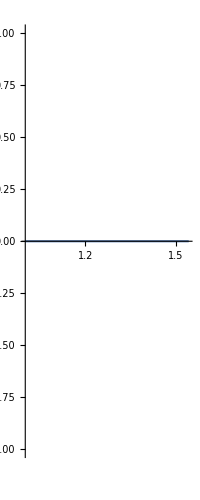

```mathematica
ParametricPlot[{( Subscript[Z, 1] /.(  eq4pt15[[2]] /. a-> 1  /. Equal-> Rule  )  ) ,( Subscript[Z, 2] /.(  eq4pt15[[3]] /. a-> 1 /. Equal-> Rule )  /. ρ-> 0)},{Subscript[t, -1],0,1}]
```

```mathematica
?ImplicitRegion
```

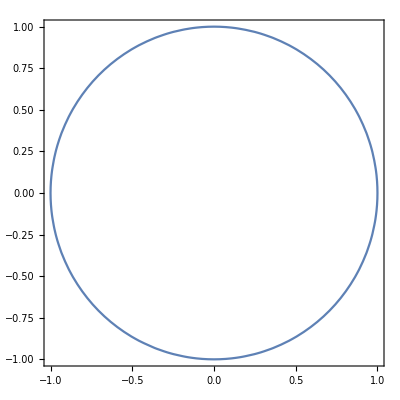
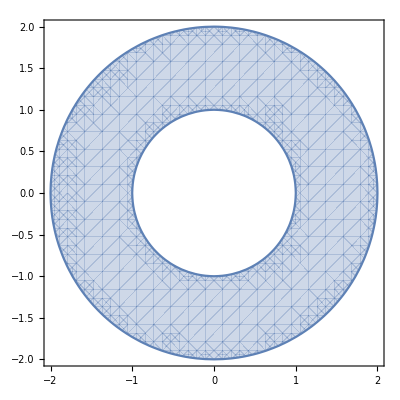

```mathematica
{ContourPlot[Subscript[Z, 1]^2+Subscript[Z, 2]^2==1,{Subscript[Z, 1],-1,1},{Subscript[Z, 2],-1,1}],RegionPlot[1<Subscript[Z, 1]^2+Subscript[Z, 2]^2<4,{Subscript[Z, 1],-2,2},{Subscript[Z, 2],-2,2}]}
```

```mathematica
?ContourPlot3D
```

```mathematica
ContourPlot3D[x+y+z,{x,y,z}∈Ball[]]
```

-Graphics3D-

```mathematica
?Ball
```

```mathematica
ImplicitRegion[hyperboloidZ0Z3Z4[[1]] ≤hyperboloidZ0Z3Z4[[2]],{Subscript[Z, 0],Subscript[Z, 3],Subscript[Z, 4]}]
```

ImplicitRegion[-Z_0^2+Z_3^2+Z_4^2≤1,{Z_0,Z_3,Z_4}]

```mathematica
hyperboloidZ0Z3Z4[[1]] 
hyperboloidZ0Z3Z4[[2]]
```

-Z_0^2+Z_3^2+Z_4^2

1

```mathematica
cone=ContourPlot3D[x^2+y^2==z^2,{x,-3,3},{y,-3,3},{z,-3,3},Mesh->None,ContourStyle->Opacity[0.3]]
```

-Graphics3D-

```mathematica
ℛ=ImplicitRegion[x^2+y^2==z^2&&x+y==2 z-1,{x,y,z}]
```

ImplicitRegion[x^2+y^2==z^2&&x+y==-1+2 z,{x,y,z}]

```mathematica
Show[{cone,DiscretizeRegion[ℛ,{{-3,3},{-3,3},{-3,3}},PrecisionGoal->100]}]
```

DiscretizeRegion::drtol: Tolerance requested by the AccuracyGoal and PrecisionGoal options is too small to be achieved. Increasing to absolute tolerance 1.54857×10^-7

-Graphics3D-

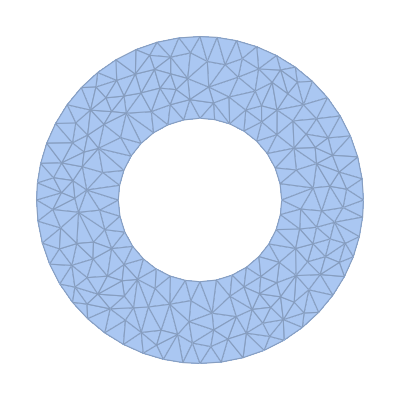

```mathematica
DiscretizeRegion[ImplicitRegion[1≤x^2+y^2≤4,{x,y}]]
```

```mathematica
?DiscretizeRegion
```

ImplicitRegion[x^6-5 x^4 y+3 x^4 y^2+10 x^2 y^3+3 x^2 y^4-y^5+y^6==0,{x,y}]

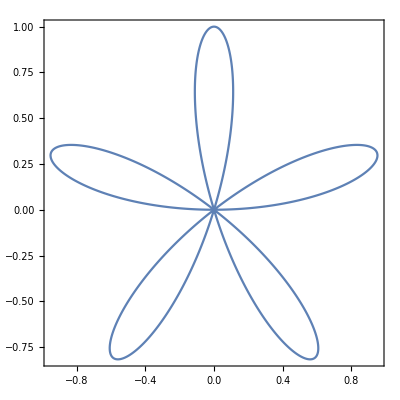

```mathematica
ℛ=ImplicitRegion[x^6-5 x^4 y+3 x^4 y^2+10 x^2 y^3+3 x^2 y^4-y^5+y^6==0,{x,y}]
RegionPlot[ℛ]
```

```mathematica
ℛ=ImplicitRegion[4≤x^2+y^2+z^2≤9,{x,y,z}]
RegionPlot3D[ℛ,PlotStyle->Opacity[0.5],PlotPoints->30]
```

ImplicitRegion[4≤x^2+y^2+z^2≤9,{x,y,z}]

-Graphics3D-

```mathematica
?ParametricPlot3D
```

```mathematica
ParametricPlot3D[{Sin[u],Cos[u],u/10},{u,0,20}]
```

-Graphics3D-

```mathematica
Clear[fig4pt8a]
fig4pt8a =
( eq4pt1[[1]] /. ( eq4pt1[[2]] /. Equal-> Rule )  /. Λ-> 3   /. Subscript[Z, 1]-> 0 /. Subscript[Z, 3]-> 0 /. Subscript[Z, 4]  -> 0  )
```

-Z_0^2+Z_2^2==1

```mathematica
fig4pt8a[[1]]
```

-Z_0^2+Z_2^2

```mathematica
ApplySides[Evaluate,fig4pt8a]
```

-Z_0^2+Z_2^2==1

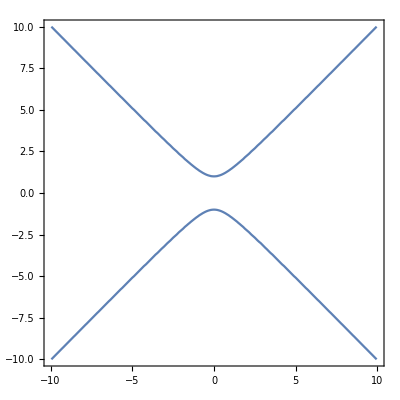

```mathematica
ContourPlot[- Subscript[Z, 0]^2+Subscript[Z, 2]^2== 1 ,{Subscript[Z, 0],-10,10},{Subscript[Z, 2],-10,10}]
```

```mathematica
?ApplySides
```

```mathematica
?ContourPlot
```

```mathematica
ContourPlot[ApplySides[Evaluate,fig4pt8a],{Subscript[Z, 0],-1,1},{Subscript[Z, 2],-1,1}]
```

-Graphics-

```mathematica
?ContourPlot
```

```mathematica
( Subscript[Z, 0] /. ( eq4pt15[[1]]  /. ρ-> 0 /.  a-> 1 /. Equal-> Rule )  ) 
( Subscript[Z, 2] /. ( eq4pt15[[3]] /. ρ-> 0  /. Equal-> Rule )  )
```

Sinh[t_-1]

0